# Some notes on Random Matrix Theory ideas for nonreactive molecules in optical lattices

### From the paper by Joseph Leva, fast generation of normally distributed random numbers.

```mathematica
vsol=Solve[Q==(u-s)^2-b(u-s)(v-t)+a(v-t)^2,v]//Simplify
```

{{v→(2 a t-√(4 a (Q-(s-u)^2)+b^2 (s-u)^2)+b (-s+u))/(2 a)},{v→(2 a t+√(4 a (Q-(s-u)^2)+b^2 (s-u)^2)+b (-s+u))/(2 a)}}

```mathematica
params1={a-> 0.19600,b->0.25472,s->0.449871,t->-0.386595,Q->0.27597};params2={a-> 0.19600,b->0.25472,s->0.449871,t->-0.386595,Q->0.27846};
```

```mathematica
Qf[u_,v_,s_,t_,a_,b_]:=(u-s)^2-b(u-s)(v-t)+a(v-t)^2
```

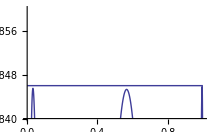

```mathematica
Plot[{Qf[u,2u √(-Log[u]),s,t,a,b],0.27597,0.27846}/.params1,{u,0,1},PlotRange->{0.2784,0.2786}]
```

Okay, so it looks like the fortran code (GOE.f) to do this should work properly with the hard-coded values for the parameters a,b,s,t,r_1,r_2

The Mathematica built-in...

```mathematica
RandomVariate[GaussianOrthogonalMatrixDistribution[1,3]]//MatrixForm
```

(-0.142372 | -0.582789 | -0.63492
-0.582789 | -2.26428 | 0.546701
-0.63492 | 0.546701 | -0.0694525)

### What is the model hamiltonian?

Let us for simplicity consider the spatial degrees of freedom associated with the nuclear positions and supress any indices associated with the electronic or spin degrees of freedom. Express the four nuclei positions in H-type Jacobi coordinates:

ρ_1=r_1-r_2

ρ_2=r_3-r_4

R=(m_3 r_3+m_4 r_4)/(m_3+m_4)-(m_1 r_1+m_2 r_2)/(m_1+m_2)

X=(m_1 r_1+m_2 r_2+m_3 r_3+m_4 r_4)/(m_1+m_2+m_3+m_4)

Let the separation between the two nonreactive molecules be the vector R. The bimolecular Hamiltonian can be written as:

H=T_R+T_ρ_1+T_ρ_2+T_X+V(ρ_1,ρ_2,R,X)

V(ρ_1,ρ_2,R,X)=[(∑_(i=1))^4 V_ext(r_i)]+V_2(ρ_1)+V_2(ρ_2)+V_2(r_13)+V_2(r_14)+V_2(r_23)+V_2(r_24)

V(ρ_1,ρ_2,R,X)=1/2 M X^2+1/2 μ_12 ρ_1^2+1/2 μ_34 ρ_2^2+1/2 μ_1234 R^2+V_2(ρ_1)+V_2(ρ_2)+V_2(r_13)+V_2(r_14)+V_2(r_23)+V_2(r_24)

For the harmonic oscillator V_ext=1/2 m ω^2 r_i^2, the center of mass motion separates completely and one can write Ψ(ρ_1,ρ_2,R,X)=Ψ_CM(X)Ψ_rel(ρ_1,ρ_2,R).

In the relative degrees of freedom we are left with:

H_rel Ψ_rel(ρ_1,ρ_2,R)=E Ψ_rel(ρ_1,ρ_2,R)

[T_R+T_ρ_1+T_ρ_2+V(ρ_1,ρ_2,R)]Ψ_rel(ρ_1,ρ_2,R)=E Ψ_rel(ρ_1,ρ_2,R)

We let the adiabatic Hamiltonian be:

H_ad=T_(R̂)+T_ρ_1+T_ρ_2+V(ρ_1,ρ_2,R)

with adiabatic eigenstates:

[T_(R̂)+T_ρ_1+T_ρ_2+V(ρ_1,ρ_2,R))]Φ_α(R;R̂,ρ_1,ρ_2)=U_α(R)Φ_α(R;R̂,ρ_1,ρ_2)

Note that the adiabatic solution depends explicitly on R̂, but only parametically on R (hence the semicolon). A channel α is defined to be open if E>U_α(R) as l_ho ≫R≫R_vdW, and closed otherwise.  Now let’s postulate that the solution can be written as

Ψ_rel(ρ_1,ρ_2,R)=∑_α Φ_α(R;R̂,ρ_1,ρ_2)ψ_α(R)

Plugging this back into Eq. EquationNumbered, we have:

H_rel∑_α Φ_α(R;R̂,ρ_1,ρ_2)ψ_α(R)=E ∑_α Φ_α(R;R̂,ρ_1,ρ_2)ψ_α(R)

Hitting this from the left with ∫ⅆ ρ_1ⅆ ρ_2ⅆ R̂  Φ_β and exploiting the orthonormality of the eigenfunctions Φ_α, we have:

∑_α ∫ⅆ ρ_1ⅆ ρ_2ⅆ R̂  Φ_β(R;R̂,ρ_1,ρ_2)H_rel Φ_α(R;R̂,ρ_1,ρ_2)ψ_α(R)=E ∑_α ∫ⅆ ρ_1ⅆ ρ_2ⅆ R̂  Φ_β(R;R̂,ρ_1,ρ_2)Φ_α(R;R̂,ρ_1,ρ_2)ψ_α(R)

Next we define:

𝒲_βα(R)=∫ⅆ ρ_1ⅆ ρ_2ⅆ R̂  Φ_β(R;R̂,ρ_1,ρ_2)H_rel Φ_α(R;R̂,ρ_1,ρ_2)

𝒲_βα(R)=∫ⅆ ρ_1ⅆ ρ_2ⅆ R̂  Φ_β(R;R̂,ρ_1,ρ_2)[T_R+T_(R̂)+T_ρ_1+T_ρ_2+V(ρ_1,ρ_2,R)]Φ_α(R;R̂,ρ_1,ρ_2)

𝒲_βα(R)=∫ⅆ ρ_1ⅆ ρ_2ⅆ R̂  Φ_β(R;R̂,ρ_1,ρ_2)[T_R+U_α(R)]Φ_α(R;R̂,ρ_1,ρ_2)

𝒲_βα(R)=∫ⅆ ρ_1ⅆ ρ_2ⅆ R̂  Φ_β(R;R̂,ρ_1,ρ_2)[T_R]Φ_α(R;R̂,ρ_1,ρ_2)+δ_βα U_α(R)

so that the relative coordinate Schrodinger equation becomes:

∑_α 𝒲_βα(R)ψ_α(R)=E ∑_α δ_βα ψ_α(R)

∑_α 𝒲_βα(R)ψ_α(R)=E ψ_β(R)

We can write this as a matrix equation:

W ψ^(i)=E_i ψ^(i)

Which looks like a Rayleigh-Ritz type variational expression, for which the exact solution vectors ψ^(i)(R)=(ψ_1^(i)(R)
ψ_2^(i)(R)
:)  give the exact energy eigenvalues E_i.

### Comments/Questions so far...

It seems to me unconventional to refer to W_nb=⟨n|Ĥ|b⟩ as “nonadiabatic couplings” because |n⟩ and |b⟩ are not adiabatic eigenstates.  They do not  correspond to the Φ_α’s above, and are not eigenstates of any adiabatic hamiltonian.  They seem to be products Ψ_n=ψ_n(R)Φ_α(R;R̂,ρ_1,ρ_2) and Ψ_b=ψ_b(R)Φ_α(R;R̂,ρ_1,ρ_2), with ψ_n a harmonic oscillator s-wave eigenfunction and ψ_b∝δ(R).

Is it fair to say that what I call Φ_α(R;R̂,ρ_1,ρ_2) correspond to R̂,ρ_1,ρ_2O and R̂,ρ_1,ρ_2B, with α∈O if U_α(R≫R_vdW)<E and α∈B if U_α(R≫R_vdW)>E?

### From a more abstract Hilbert space...

Let’s start with a ket notation where the full eigenstate of the complete Hamiltonian is written:

Ψ=∑_α ψ_α α_R

where ψ_α lives in the part of the Hilbert space corresponding to the separation coordinate R.  α_R is an eigenstate of the adiabatic Hamiltonian that depends parametrically on R:

H_ad α_R=U_α α_R

Inserting complete sets of states

∫ⅆ Ω'∫ⅆΩΩ'Ω' H_ad Ω Ωα_R=∫ⅆΩ U_α(R)Ω Ωα_R

If H_ad is a local operator, then Ω' H_ad Ω=δ(Ω'-Ω)H_ad(R;Ω).  Furthermore, let Φ_α(R;Ω)=Ωα_R

∫ⅆΩΩH_ad(R;Ω)Φ_α(R;Ω)=∫ⅆΩ U_α(R)Φ_α(R;Ω)Ω

H_ad(R;Ω)Φ_α(R;Ω)=U_α(R)Φ_α(R;Ω)

Now, returning to the full Hamiltonian:

H=T_R+T_ρ_1+T_ρ_2+T_X+V(ρ_1,ρ_2,R,X)

H=T_R+(T_(R̂)+T_ρ_1+T_ρ_2+T_X+V(ρ_1,ρ_2,R,X))

Now the question is how does one arrive at Eq. (1) of the PRL from the Hamiltonian above and the basic expansion Ψ=∑_α ψ_α α_R?

Now what seems appropriate to me is to expand:

ψ_α=∑_n c_nα ψ_n+∑_b c_bα ϕ_b

so that in each adiabatic channel, we have an expansion over oscillator states and bound states:

Ψ=∑_α ψ_α α_R=∑_α (∑_b c_bα ϕ_b+∑_n c_nα ψ_n)α_R

Ψ=∑_α ψ_α α_R=∑_αb c_bα ϕ_b α_R+∑_αn c_nα ψ_n α_R

Normalization of the state would suggest:

ΨΨ=1=∑_(α'b'α b) (c*)_b'α' c_(b α)ϕ_b'ϕ_bα'α+∑_(α'b'α n) (c*)_b'α' c_(n α)ϕ_b'ψ_nα'α+∑_(α'n'α b) (c*)_n'α' c_(b α)ψ_n'ϕ_bα'α+∑_(α'n'α n) (c*)_n'α' c_(n α)ψ_n'ψ_nα'α

ΨΨ=1=∑_(α'b'α b) (c*)_b'α' c_(b α)δ_(b,b')δ_(α,α')+∑_(α'b'α n) (c*)_b'α' c_(n α)ϕ_b'ψ_n δ_(α,α')+∑_(α'n'α b) (c*)_n'α' c_(b α)ψ_n'ϕ_b δ_(α,α')+∑_(α'n'α n) (c*)_n'α' c_(n α)δ_(n,n')δ_(α,α')

ΨΨ=1=∑_(α b) (|c_(b α)|)^2+∑_(α n) (|c_(n α)|)^2+∑_(b'α n) (c*)_b'α c_(n α)ϕ_b'ψ_n+∑_(n'α b) (c*)_n'α c_(b α)ψ_n'ϕ_b

The overlap between the tightly bound state and the oscillator state is going to be proportional to ψ_n(0).  Write: ϕ_b'ψ_n=K_b' ψ_n(0)

ΨΨ=1=∑_(α b) (|c_(b α)|)^2+∑_(α n) (|c_(n α)|)^2+∑_(b'α n) (c*)_b'α c_(n α)K_b' ψ_n(0)+∑_(n'α b) (c*)_n'α c_(b α)K_b ψ_n'(0)

Consider the set of basis states (as described in the supplement of the PRL):

Ψ_n=ψ_n α_R       | n=0,1,2,...

Ψ_b=ϕ_b α_R       | b=0,1,2,...

where ψ_n is an oscillator state and ϕ_b is a bimolecular bound state.  The explicit coordinate space representation is:

Ψ_n(R,Ω)=Rψ_n Ωα_R=ψ_n(R)Φ_α(R;Ω)

Ψ_b(R,Ω)=Rϕ_b Ωα_R=ϕ_b(R)Φ_α(R;Ω)

with bimolecular bound state is highly localized near R=0, i.e. ϕ_b∝δ(R).

H=T_R+(T_(R̂)+T_ρ_1+T_ρ_2+T_X+V(ρ_1,ρ_2,R,X))

So, what does the completeness relation look like for these basis states?  They are not orthonormal.  Does it make sense to write:

1=∑_n Ψ_nΨ_n+∑_b Ψ_bΨ_b

For example, is 1^2=1?

1^2=(∑_n Ψ_nΨ_n+∑_b Ψ_bΨ_b)(∑_n' Ψ_n'Ψ_n'+∑_b' Ψ_b'Ψ_b')

1^2=(∑_n Ψ_nΨ_n+∑_b Ψ_bΨ_b)(∑_n' Ψ_n'Ψ_n'+∑_b' Ψ_b'Ψ_b')

### scratch work...

We could choose to write:

ψ_α=∑_n c_n^α ψ_n(R)+∑_b c_b^α ψ_b(R)

Consider for a moment the solutions in the absence of off-diagonal couplings.  In that case:

𝒲_βα(R)=δ_βα 𝒲_α(R)=(∫ⅆ ρ_1ⅆ ρ_2ⅆ R̂  Φ_α(R;R̂,ρ_1,ρ_2)[T_R]Φ_α(R;R̂,ρ_1,ρ_2)+U_α(R))δ_βα

For reference, in a hyperspherical description, we would write:

[-ℏ^2/(2μ)∂^2/(∂R^2)+H_ad(R,Ω)]Ψ(R,Ω)=E Ψ(R,Ω)

H_ad=(Λ^2+(3N-4)(3N-6)/4)/(2μ R^2)+V(R,Ω)